# Implementation of Object-Oriented Patterns Design Patterns in WL

## Introduction

This document presents a particular style of programming in Mathematica that allows the application of the Object-Oriented Programming (OOP) paradigm (to a point). The approach does not require the use of preliminary implementations, packages, or extra code. Using the OOP paradigm is achieved by following a specific programming style and conventions with native, fundamental programming constructs in Mathematica’s programming language.

We can say that the Object-oriented paradigm came to maturity with OOP Design Patterns, which were introduced in [5]. The book [5] describes Design Patterns as software architectural solutions obtained from analysis of successful software products. Design Patterns help overcome limitations of programming languages, give higher level abstractions for program design, and provide design transformation guidance. Because of extensive documentation and examples, Design Patterns help knowledge transfer and communication between developers. Because of these observations it is much better to emulate OOP in Mathematica through Design Patterns than through emulation of OOP objects.

It is beyond the scope of this document to give an OOP introduction to Design Patterns. For detailed description of the patterns implemented and discussed we are going to refer to [5]. (All of the design patterns considered in this document have entries in Wikipedia.)

The following Venn-like diagram shows the large context of patterns. This document is for the patterns in the dark red area (“Design Patterns by GoF”).

-Graphics-

### Design patterns history

In 1975 the architect Christopher Alexander et al., [2], introduced a pattern language for architectural solutions. Alexander’s book “The Timeless Way of Building”, [3], is the more fundamental one -- some sort of philosophical prequel of [1] and [2].

The computer scientists Kent Beck and Ward Cunningham started applying these ideas in software architecture in 1987 and presented results in the conference Object-Oriented Programming, Systems, Languages, and Applications (OOPSLA) -- see [4].

In 1995 the book by Gamma et al. “Design Patterns: Elements of Reusable Object-Oriented Software” provided a catalog of well researched and documented design patterns and that brought design patterns and pattern languages great popularity and acceptance. In 2005 ACM SIGPLAN awarded that year’s Programming Language Achievements Award to the authors. The authors are of often references ad the “Gang of Four” (GoF).

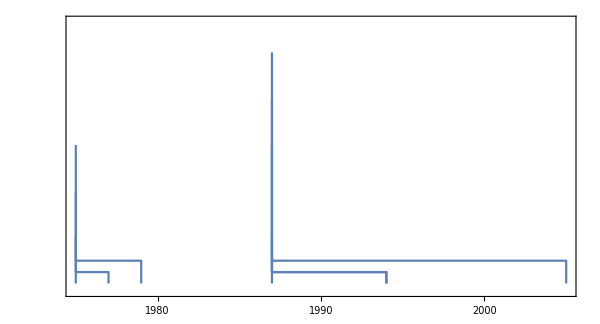

```mathematica
patternsHistory=Dataset[Association/@{{"Persons"->{"Christopher Alexander","Sara Ishikawa", "Murray Silverstein"},"Date"->"1977","EventType"->"book release","EventName"->"'A Pattern Language - Towns, Buildings, Construction'\nbook by Alexander et al.","note"->"generative grammar"},
{"Persons"->{"Christopher Alexander"},"Date"->"1979","EventType"->"book release","EventName"->"'The Timeless Way of Building'\nbook by Alexander","note"->"concepts, the quality without a name"},
{"Persons"->{"Kent Beck","Ward Cunningham"},"Date"->"1987","EventType"->"articles","EventName"->"OOPSLA articles by Beck and Cunningham"},{"Persons"->{"GoF"},"Date"->"1994","EventType"->"book release","EventName"->"'Design Patterns: Elements of Reusable Object-Oriented software'\nbook by GoF"},
{"Persons"->{"Christopher Alexander","Schlomo Angel","Sara Ishikawa", "Murray Silverstein","Danny Angel"},"Date"->"1975","EventType"->"book release","EventName"->"'The Oregon experiment'\nbook by Alexander et al."},
{"Persons"->{"many"},"Date"->"1994","EventType"->"conference started","EventName"->"'Pattern Languages of Programming' conference started"},
{"Persons"->"ACM SIGPLAN","Date"->"2005","EventType"->"award","EventName"->"SIGPLAN Programming Language Achivements Award to GoF"}}];
tlData=Transpose[{Normal[patternsHistory[All, "EventName"]] , Map[DateObject[DateList[{#, {"Year"}}]] &, Normal[ patternsHistory[All, "Date"]]]}];
tlData=Association[Rule@@@tlData];
TimelinePlot[tlData]
AutoCollapse[]
```

.

### Design Patterns structure

The OOP Design Patterns in [5] are classified in three groups: creational, structural, and behavioral. The application of the structural and behavioral patterns in a design brings the need for the application creational patterns. In this document we are mostly interested in the structural and behavioral patterns, since in Mathematica creation of objects is much more immediate than in languages like C++ and Java.

The OOP Design Patterns are presented in a certain standard form. The form has four essential elements, [5],  pattern name, problems for which the pattern is applicable, solution description, consequences of applying the pattern. The book [5] presents each pattern in the following form:

Pattern name and classification

Intent

Also known as

Motivation

Applicability

Structure

Participants

Collaborations

Consequences

Implementation

Sample code

Known uses

Related patterns

All enumerated parts are considered important.

(Because [5] is also structured as a manual it can be very difficult to read at first if the reader has little exposure to OOP. )

We are not going to follow the template given above. For each considered design pattern we are going to cite the intent from [5], provide code in Mathematica, and discuss applications inside Mathematica or with Mathematica.

### Narration

It is accepted in technical and scientific writings to use plural voice or make neutral objective-like statements. Since Design Patterns were (and are) discovered in successful software that narrative style seems applicable. Understanding and applying Design Patterns, though, rely on extensive experience of software systems programming, maintaining, and utilization. Trying to apply them within a functional and rule based programming language like Mathematica inevitably requires a more personal perspective of programming and software goals.

Because of these observations I am going to use first person narration where objectivity cannot be fully guarantied, where there are multiple choices for the design solution, or where the design justification is based on past experience.

It seems appropriate at this point to discuss my past programming experiences.

### Personal experiences with Design Patterns

This section is mostly to provide some background of why want to discuss the implementation of Design Patterns in Mathematica and why I think they are useful to apply in large development projects.

#### Large scale air-pollution modeling

In 2001 I obtained my Ph.D. in applied mathematics for writing an OOP framework for the numerical simulation of large scale air pollution (and writing related articles and thesis). Air pollution simulations over continents like Europe are grand challenge problems that encompass several scientific sub-cultures: computational fluid dynamics, computational chemistry, computational geometry, and parallel programming. I did not want to just a produce an OOP framework for addressing this problem -- I wanted to produce the best OOP framework for the set of adopted methods to solve these kind of problems.

One way to design such a framework is to use Design Patterns and did so using C++. Because I wanted to bring sound arguments during my Ph.D. defense that I derived on of the best possible designs, I had to use some formal method for judging the designs made with Design Patterns. I introduced the relational algebra of the Database theory into the OOP Design Patterns, and I was able to come up with some sort of proof why the framework written is designed well. More practically this was proven by developing, running, and obtaining results with different numerical methods for the air-pollution problems.

In my Ph.D. thesis I showed how to prove that Design Patterns provide robust code construction through the theory Relational Databases, [13].

(One of the key concepts and goals in OOP is reuse. In OOP when developing software we do not want changes in one functional part to bring domino effect changes in other parts. Design Patterns help with that. Relational Databases were developed with similar goals in mind -- we want the data changes to be confined to only one relevant place. We can view OOP code as a database, the signatures of the functions being the identifiers and the function bodies being the data. If we bring that code-database into a third normal form we are going to achieve the stability in respect to changes desired in OOP. We can interpret the individual Design Patterns as bringing the code into such third normal forms for the satisfaction of different types of anticipated code changes.)

While working at Wolfram Research Inc. I re-implemented that framework in order to demonstrate the capabilities of gridMathematica. (And that demo became quite popular and presented in different conferences in 2006 and 2007.) The re-implementation in top-level Mathematica code was done using Design Patterns, [6].

#### Numerical integration

After joining Wolfram Research, Inc. I designed, developed, and documented the (large) numerical integration framework of NIntegrate. The implementation was done using both C and Mathematica and I used Design Patterns with both languages.

#### Other applications

In the last 9 years I have worked in the field of machine learning and data mining. I have used Design Patterns to implement digital media search engines, recommendation engines, and a broadcast scheduler. I use Design Patterns when I program larger projects in Mathematica or R and I always use Design Patterns when I program in Java and C++.

### Small example of Design Patterns in Mathematica

After I answered the question “Import and Plot Git Commit History” in Mathematica StackExchange, I realized that the problem and desired functionalities presented there are both complex enough and simple enough to make a good example of object-oriented implementation in Mathematica using Design Patterns. The package GitHubPlots.m, [7], provides are “standard” implementation, and the package GitHubDataObjects.m, [8], provides an implementation with Design Patterns.

A separate document explaining that implementation is ....

## UML diagrams

The Unified Modeling Language (UML) diagrams used in this document are more basic than the ones used in [5], but provide (I hope) a sufficient visual aid. They are generated over the Mathematica implementation code of the Design Patterns. See the package UMLDiagramGeneration.m, [10].

In UML abstract classes and operations (methods) are given in slanted font (italic). Inheritance is depicted with a line with unfilled triangle pointing to the parent class.

Here is an example:

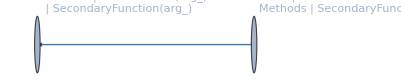

```mathematica
Module[{CLASSHEAD},
Parent[s_]["MainFunction"[arg_]]:=Print["Parent:mf"arg];
Parent[s_]["SecondaryFunction"[arg_]]:=Print["Parent:sf",arg];
Child[d_][s_]:=Block[{CLASSHEAD=Child},Parent[d][s]];
Child[s_]["SecondaryFunction"[arg_]]:=Print["Child:sf",arg];
UMLClassGraph[{Parent,Child},{Parent->{Parent,"SecondaryFunction"}}]
]
ClearAll[Parent,Child]
AutoCollapse[]
```

Here are simplified versions of chart above:

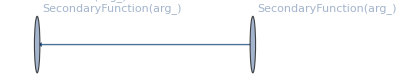

```mathematica
Module[{CLASSHEAD},
Parent[s_]["MainFunc"[arg_]]:=Print["Parent:mf"arg];
Parent[s_]["SecondaryFunction"[arg_]]:=Print["Parent:sf",arg];
Child[d_][s_]:=Block[{CLASSHEAD=Child},Parent[d][s]];
Child[s_]["SecondaryFunction"[arg_]]:=Print["Child:sf",arg];
UMLClassGraph[{Parent,Child},{Parent->{Parent,"SecondaryFunction"}},"EntityColumn"->False]
]
ClearAll[Parent,Child]
AutoCollapse[]
```

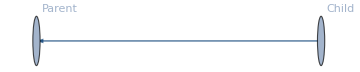

```mathematica
Graph[{Framed[Style["Child",Bold]]->Framed[Style["Parent",Bold,Italic]]},VertexLabels->"Name",ImageSize->Medium,EdgeShapeFunction->UMLInheritanceEdgeFunc]
AutoCollapse[]
```

The package UMLDiagramGeneration.m can be loaded with the command:

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/UMLDiagramGeneration.m"]
```

## Preliminary concepts

Here is a list of notions I assume the readers of this document to be familiar with:

S-expressions

Closures

Dynamic and lexical scoping

Inheritance & Delegation

DownValues, SubValues

## Class inheritance

Inheritance is the fundamental implementation to understand. This section shows delegation to a more abstract class. The section “Template Method” shows how to make the ancestor delegation even more useful.

Consider the following example. We have three classes C0, C1, and C2. The class C1 inherits C0, C2 inherits C1. We write this as C0←C1←C2.

### UML diagram

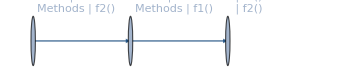

```mathematica
UMLClassGraph[{C0,C1,C2}, {}, "Abstract" -> {},"EntityColumn"->True, VertexLabelStyle -> "Text", ImageSize -> Medium]
AutoCollapse[]
```

### Implementation

The basic idea is to use symbols` sub-values.

```mathematica
Clear[C0,C1,C2]
```

```mathematica
C0[d_]["Data"[]]:=d;
C0[{a_,b_,c_,___}]["f0"[]]:=a;
C0[{a_,b_,c_,___}]["f1"[]]:=a+b;
C0[{a_,b_,c_,___}]["f2"[]]:=a+b+c;
```

```mathematica
C1[d_][s_]:=C0[d][s]
C1[{a_,b_,c_}]["f1"[]]:=a*b;
```

```mathematica
C2[d_][s_]:=C1[d][s]
C2[{a_,b_,c_}]["f2"[]]:=a^b;
```

### Experiments

Here we define a C2 object:

```mathematica
obj=C2[{a,b,c}]
```

C2[{a,b,c}]

This invokes C1' s definition

```mathematica
obj["f1"[]]
```

a b

This invokes C2's definition:

```mathematica
obj["f2"[]]
```

a^b

Finally, this invokes C0’s definition:

```mathematica
obj["f0"[]]
```

a

Let us look into more detail of what is happening. We have made an object of the class C2, meaning we have an expression with head C2 and some data inside the expression:

```mathematica
C2[{123,z2, z3}]
```

C2[{123,z2,z3}]

There are sub-value rules for C2:

```mathematica
SubValues[C2]
```

{HoldPattern[C2[{a_,b_,c_}][f2[]]]:>a^b,HoldPattern[C2[d_][s_]]:>C1[d][s]}

The first C2 sub-value rule is specialized, it specifies the S-expression with head C2 and one argument, a list of arbitrary three elements, would give a result combining two of them when applied to "f2"[]. The second sub-value rule is more general, an expression with head C2 and one element that when applied over s_ is directed to change its head to C1 and use C1’s sub-values. Because Mathematica gives precedence to more specialized patterns we effectively have delegation of behavior to a more abstract entity.

Here is one more example:

```mathematica
C0[{1343,1,3}]["f1"[]]
```

1344

```mathematica
C2[{1343,1,3}]["f1"[]]
```

1343

It is instructive to look at the evaluation trace of C2 and C1 expressions called over “f1”. For example:

```mathematica
C2[{1343,1,3}]["f1"[]]//Trace
```

{C2[{1343,1,3}][f1[]],C1[{1343,1,3}][f1[]],1343 1,1343}

## Static class inheritance

The inheritance implementation in the previous section was achieved through dynamic resolution of the symbols sub-value rules in order to invoke the corresponding implementation for a given signature. We can implement static inheritance by using direct manipulation of sub-values.

The idea of the static inheritance is simple: (i) we take the sub-values of the parent and assign them to the child, and (ii) we change one or several of child sub-values to correspond to the desired changes of behavior.

Note that the classes have the same definitions of the “delegated” function members. Using static inheritance we have saved copying and assigning code.

### UML diagram

```mathematica
Row[Riffle[UMLClassNode/@{C0,C1,C2}," "]]
AutoCollapse[]
```

Class | C0
Methods | Data[]
 | f0[]
 | f1[]
 | f2[] Class | C1
Methods | Data[]
 | f0[]
 | f2[]
 | f1[] Class | C2
Methods | Data[]
 | f0[]
 | f1[]
 | f2[]

### Implementation

```mathematica
Clear[C0,C1,C2]
```

```mathematica
C0[d_]["Data"[]]:=d;
C0[{a_,b_,c_,___}]["f0"[]]:=a;
C0[{a_,b_,c_,___}]["f1"[]]:=a+b;
C0[{a_,b_,c_,___}]["f2"[]]:=a+b+c;
```

Static inheritance C0 -> C1:

```mathematica
SubValues[C1]=ReplaceRepeated[SubValues[C0],C0->C1];
```

```mathematica
pos=Position[First/@SubValues[C1],"f1"[___],∞][[1,1]];
SubValues[C1]=Drop[SubValues[C1],{pos}];
C1[{a_,b_,c_,___}]["f1"[]]:=a*b;
```

Static inheritance C1-> C2:

```mathematica
SubValues[C2]=ReplaceRepeated[SubValues[C1], C1-> C2];
```

```mathematica
pos=Position[First/@SubValues[C2],"f2"[___],∞][[1,1]];
SubValues[C2]=Drop[SubValues[C2],{pos}];
C2[{a_,b_,c_,___}]["f2"[]]:=a^b;
```

pos is for the positions of the overridden methods.

### Experiments

Here we define a C2 object:

```mathematica
obj=C2[{a,b,c}];
```

Functions borrowed from C0:

```mathematica
obj["Data"[]]
obj["f0"[]]
```

{a,b,c}

a

Functions borrowed from C1:

```mathematica
obj["f1"[]]
```

a b

And finally genuine the C2 function:

```mathematica
obj["f2"[]]
```

a^b

It is instructional to see the definitions of the symbols defined above.

```mathematica
?C0
```

Global`C0

C0[d_][Data[]]:=d
 
C0[{a_,b_,c_,___}][f0[]]:=a
 
C0[{a_,b_,c_,___}][f1[]]:=a+b
 
C0[{a_,b_,c_,___}][f2[]]:=a+b+c

## Template Method

Function invocation by delegation through inheritance is a good first step but by itself is not enough to employ OOP in a powerful way. The next step is to provide an invariant algorithm in the abstract class and delegate the concrete operations of that invariant algorithm to the descendants. This is nicely demonstrated with the design pattern Template Method which is a fundamental micro-architectural solution in OOP.

Here is the “intent” of Template Method from [5]:

Define the skeleton of an algorithm in an operation, deferring some steps to subclasses. Template Method lets subclasses redefine certain steps of an algorithm without changing the algorithm’s structure.

### Motivational example

Mathematica has the function Inner that perfectly demonstrates the usefulness of Template-Method-like functionality code breakdown.

Here is an algorithm “skeleton” made with Inner:

```mathematica
in1=Inner[op1,{a,b,c},{x,y,z},op2]
```

op2[op1[a,x],op1[b,y],op1[c,z]]

We can easily derive different algorithms by replacing the symbols op1 and op2 with concrete functions:

```mathematica
Inner[Times,{a,b,c},{x,y,z},Norm@*List]
```

√(Abs[a x]^2+Abs[b y]^2+Abs[c z]^2)

Alternatively, we can consider varying the data arguments of Inner:

```mathematica
in2=Inner[op1,Mat@@@Map[Array[#,{2,1}]&,{a,b}],Mat@@@Map[Array[#,{1,2}]&,{x,y}],op2]
```

op2[op1[Mat[{a[1,1]},{a[2,1]}],Mat[{x[1,1],x[1,2]}]],op1[Mat[{b[1,1]},{b[2,1]}],Mat[{y[1,1],y[1,2]}]]]

These concrete implementations of op1 and op2 provide different functionalities depending on the data types:

```mathematica
Block[{op1,op2},
op1[x_?AtomQ,y_?AtomQ]:=x**y;
op1[x_Mat,y_Mat]:=(List @@ x).( List @@ y);
op2[args___]:=Plus[args];
op2[args:(_List...)]:=MatrixForm[Plus[args]];
Grid[{{"in1:",in1},{"in2:",in2}},Dividers->All]
]
```

in1: | a**x+b**y+c**z
in2: | (a[1,1] x[1,1]+b[1,1] y[1,1] | a[1,1] x[1,2]+b[1,1] y[1,2]
a[2,1] x[1,1]+b[2,1] y[1,1] | a[2,1] x[1,2]+b[2,1] y[1,2])

Note that for _Mat objects the code above returns the result in MatrixForm.

### UML diagram

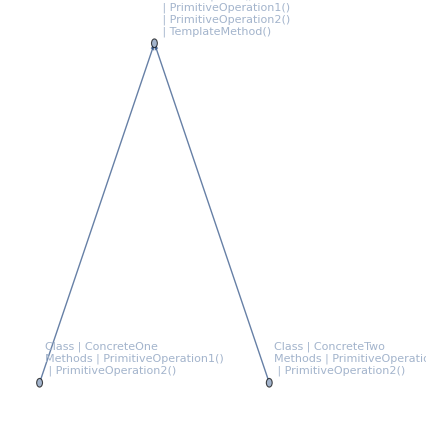

```mathematica
UMLClassGraph[{AbstractClass,ConcreteOne,ConcreteTwo}, {AbstractClass -> {"PrimitiveOperation1", "PrimitiveOperation2"}}, "Abstract" -> {AbstractClass}, VertexLabelStyle -> "Text", ImageSize -> Medium,GraphLayout->"LayeredEmbedding"]
AutoCollapse[]
```

### Implementation

For the implementation of Template Method we basically combine sub-values with Block's dynamic scoping.

```mathematica
Clear[AbstractClass,ConcreteOne,ConcreteTwo];
```

```mathematica
CLASSHEAD=AbstractClass;
AbstractClass[d_]["Data"[]]:=d;
AbstractClass[d_]["PrimitiveOperation1"[]]:=d[[1]];
AbstractClass[d_]["PrimitiveOperation2"[]]:=d[[2]];
AbstractClass[d_]["TemplateMethod"[]]:=CLASSHEAD[d]["PrimitiveOperation1"[]]+CLASSHEAD[d]["PrimitiveOperation2"[]]
```

```mathematica
ConcreteOne[d_][s_]:=Block[{CLASSHEAD=ConcreteOne},AbstractClass[d][s]]
ConcreteOne[d_]["PrimitiveOperation1"[]]:=d[[1]];
ConcreteOne[d_]["PrimitiveOperation2"[]]:=d[[1]]*d[[2]];
```

```mathematica
ConcreteTwo[d_][s_]:=Block[{CLASSHEAD=ConcreteTwo},AbstractClass[d][s]]
ConcreteTwo[d_]["PrimitiveOperation1"[]]:=d[[1]];
ConcreteTwo[d_]["PrimitiveOperation2"[]]:=d[[3]]^d[[2]];
```

### Experiments

```mathematica
t=AbstractClass[{a,b,c}]
t["Data"[]]
t["TemplateMethod"[]]
```

AbstractClass[{a,b,c}]

{a,b,c}

a+b

```mathematica
c1=ConcreteOne[{a,b,c}]
c1["Data"[]]
c1["TemplateMethod"[]]
```

ConcreteOne[{a,b,c}]

{a,b,c}

a+a b

```mathematica
c2=ConcreteTwo[{a,b,c}]
c2["Data"[]]
c2["TemplateMethod"[]]
```

ConcreteTwo[{a,b,c}]

{a,b,c}

a+c^b

It is instructive to see the trace of the invocations.

This call uses a method defined in the abstract class:

```mathematica
c1["Data"[]]//Trace//ColumnForm
```

{c1,ConcreteOne[{a,b,c}]}
ConcreteOne[{a,b,c}][Data[]]
Block[{CLASSHEAD=ConcreteOne},AbstractClass[{a,b,c}][Data[]]]
{CLASSHEAD=ConcreteOne,ConcreteOne}
{AbstractClass[{a,b,c}][Data[]],{a,b,c}}
{a,b,c}

This trace shows the call for the abstract algorithm (template method) for a concrete class object that invokes the primitive operation defined in that concrete class.

```mathematica
c1["TemplateMethod"[]]//Trace
```

{{c1,ConcreteOne[{a,b,c}]},ConcreteOne[{a,b,c}][TemplateMethod[]],Block[{CLASSHEAD=ConcreteOne},AbstractClass[{a,b,c}][TemplateMethod[]]],{CLASSHEAD=ConcreteOne,ConcreteOne},{AbstractClass[{a,b,c}][TemplateMethod[]],CLASSHEAD[{a,b,c}][PrimitiveOperation1[]]+CLASSHEAD[{a,b,c}][PrimitiveOperation2[]],{{{CLASSHEAD,ConcreteOne},ConcreteOne[{a,b,c}]},ConcreteOne[{a,b,c}][PrimitiveOperation1[]],{a,b,c}⟦1⟧,a},{{{CLASSHEAD,ConcreteOne},ConcreteOne[{a,b,c}]},ConcreteOne[{a,b,c}][PrimitiveOperation2[]],{a,b,c}⟦1⟧ {a,b,c}⟦2⟧,{{a,b,c}⟦1⟧,a},{{a,b,c}⟦2⟧,b},a b},a+a b},a+a b}

### Other concrete examples

#### Template Method version of the motivational example

Using the motivational example let us implement a class hierarchy adhering to the Template Method that provides an invariant algorithm and different specializations of its concrete operations.

```mathematica
CLASSHEAD=AbstractInner;
AbstractInner[d___]["TemplateMethod"[x_,y_]]:=Inner[CLASSHEAD[d]["op1"[#1,#2]]&,x,y,CLASSHEAD[d]["op2"[##]]&];
AtomInner[d___][s_]:=Block[{CLASSHEAD=AtomInner},AbstractInner[d][s]];
AtomInner[d___]["op1"[x_,y_]]:=NonCommutativeMultiply[x,y];
AtomInner[d___]["op2"[args___]]:=Plus[args];
MatInner[d___][s_]:=Block[{CLASSHEAD=MatInner},AbstractInner[d][s]];
MatInner[d___]["op1"[x_,y_]]:=Dot[List@@x,List@@y];
MatInner[d___]["op2"[args___]]:=MatrixForm[Plus[args]];
```

```mathematica
obj1=AtomInner["Atoms"];
obj1["TemplateMethod"[{a,b},{x,y}]]
```

a**x+b**y

```mathematica
obj2=MatInner["Mat objects"];
obj2["TemplateMethod"[
{Mat[{a1,b1},{a2,b2}],Mat[{A1,B1},{A2,B2}]},
{Mat[{x},{y}],Mat[{X},{Y}]}]
]
```

(a1 x+A1 X+b1 y+B1 Y
a2 x+A2 X+b2 y+B2 Y)

Note that there is the question of the right selection of a Template Method descendant for a given pair of argument objects. There are creational Design Patterns that address these type of problems (Abstract Factory, Factory Method); see [5]. In Mathematica we can easily address that problem with pattern matching.

#### GitHubData

The functionality of the main GitHub data class in [5] GitHubData is modified with the descendant object GitHubDataMessageHyperlinks
 so the ticks of the plots have hyperlinks to the github.com pages corresponding to the commits. The template method algorithm is the method “Plot”, the primitive operations are “ParseData”, “TickLabels”, and “DatePoints”. The class GitHubDataMessageHyperlinks provides its own implementation of “TickLabels” (making the ticks click-able).

## Strategy

Here is intent of the design pattern Strategy from [5]:

Define a family of algorithms, encapsulate each one, and make them interchangeable. Strategy lets the algorithm vary independently from clients that use it.

Generally Strategy’s structure is not needed in Mathematica because of the functional programming paradigm support and pattern matching of function signatures. Conceptually Strategy is applied all the time, e.g. second order functions or writing functions with arguments being other functions.

Nevertheless, we are going to give an implementation of Strategy that might be useful when prototyping in Mathematica and considering moving to production languages like C++ or Java. The implementation is essentially similar to the one given in the section “Inheritance”. Here we are going to endow it with additional code to facilitate the use of the class hierarchy within several Design Patterns.

### UML diagram

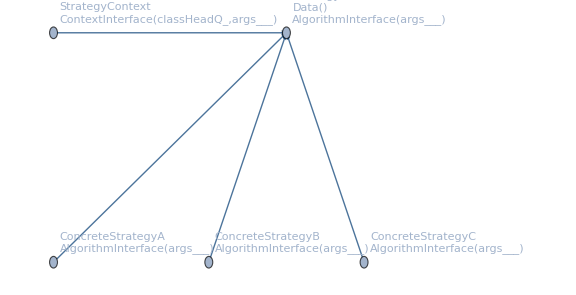

```mathematica
gr=UMLClassGraph[{StrategyContext,Strategy,ConcreteStrategyA,ConcreteStrategyB,ConcreteStrategyC},{Strategy->{"AlgorithmInterface"}},{StrategyContext->Strategy},"Abstract"->{Strategy},"EntityColumn"->False,VertexLabelStyle->"Text",ImageSize->Large,VertexCoordinates->{{0.,0.},{1.,2/3},{2/3,0.},{4/3,0.},{0,2/3}}]
AutoCollapse[]
```

### Implementation

```mathematica
Clear[Strategy,StrategyContext,"ConcreteStrategy*"]
```

```mathematica
CLASSHEAD=Strategy;
Strategy[d__]["Data"[]]:=d
Strategy[d__]["AlgorithmInterface"[args___]]:=None;
ConcreteStrategyA[d__][s_]:=Block[{CLASSHEAD=ConcreteStrategyA},Strategy[d][s]];
ConcreteStrategyA[d__]["AlgorithmInterface"[args___]]:=(StringJoin@@Riffle[Map[ToString,{args}],","]);
ConcreteStrategyB[d__][s_]:=Block[{CLASSHEAD=ConcreteStrategyB},Strategy[d][s]];
ConcreteStrategyB[d__]["AlgorithmInterface"[args___]]:=Length/@{args};
ConcreteStrategyC[d__][s_]:=Block[{CLASSHEAD=ConcreteStrategyC},Strategy[d][s]];
ConcreteStrategyC[d__]["AlgorithmInterface"[args___]]:=Thread[{args}->Range[Length[{args}]]];
```

```mathematica
StrategyContext[sobj_]["ContextInterface"[classHeadQ_,args___]]:=Print[If[classHeadQ,ToString[Head[sobj]]<>" : ",""],sobj["AlgorithmInterface"[args]]];
```

### Experiments

Here we create an object of StrategyContext using a concrete strategy object:

```mathematica
obj1=StrategyContext[ConcreteStrategyA[Unique[]]]
```

StrategyContext[ConcreteStrategyA[$32]]

```mathematica
obj1["ContextInterface"[False,1,b,Range[3]]]
```

1,b,{1, 2, 3}

Here we simply replace one concrete strategy with another concrete strategy:

```mathematica
obj2=ReplacePart[obj1,1->ConcreteStrategyC[Unique[]]];
obj2["ContextInterface"[True,1,b,Range[3]]]
```

ConcreteStrategyC : {1→1,b→2,{1,2,3}→3}

We can do something more elaborated and create a StrategyContext object initialized with the abstract class Strategy and change its behavior by changing the value of the symbol Strategy. This way we are going to emulate the so called substitution principle in OOP.

```mathematica
obj3=StrategyContext[Strategy[Unique[]]];
Block[{Strategy=#},obj3["ContextInterface"[True,a,b,c]]]&/@ToExpression/@Names["ConcreteStrategy*"]
```

ConcreteStrategyA : a,b,c

ConcreteStrategyB : {0,0,0}

ConcreteStrategyC : {a→1,b→2,c→3}

{Null,Null,Null}

### Uses in Mathematica

As it was mentioned above all second order functions (Map, Fold, Nest, FixedPoint, etc.) provide good examples of the functionality achieved by Strategy. Further, very often the algorithms specified by the Method option in different functions can be seen -- at least conceptually -- as playing within the Strategy design pattern.

### Other concrete examples

The plotting functionality of the main GitHub data class in [5] GitHubData given by the method “Plot” is changed through the Strategy design pattern. The data member “PlotFunction” can be set to one of the functions GHDDateListPlot, GHDBarPlot, or GHDGraphics3D. In this way different plots are derived for the representation of the ingested GitHub data.

## Composite

The design pattern Composite allows the treatment of multiple objects as one. More formally Composite’s intent is, [5]:

Compose objects into tree structures to represent part-whole hierarchies. Composite lets clients treat individual objects and compositions of objects uniformly.

A typical example is moving one or several desktop icons by mouse selection and dragging.

### UML diagram

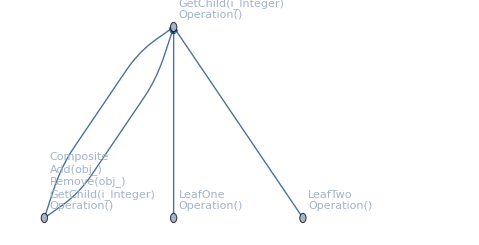

```mathematica
UMLClassGraph[{Component,LeafOne,LeafTwo,Composite}, {Component -> {"Operation","Add", "Remove","GetChild"}}, {},{Composite<->Component},"Abstract" -> {Component},"EntityColumn"->False, VertexLabelStyle -> "Text", ImageSize -> Medium,GraphLayout->"LayeredEmbedding"]
AutoCollapse[]
```

### Implementation

```mathematica
Clear[Component,LeafOne,LeafTwo,Composite];
```

```mathematica
CLASSHEAD=Component;
Component[d_,sm_]["Submethods"[]]:=sm;
Component[{a_,b_,c_},sm_]["Add"[obj_]]:=CLASSHEAD[{a,b,c},sm]["Add"[obj]];
Component[{a_,b_,c_},sm_]["Remove"[obj_]]:=CLASSHEAD[{a,b,c},sm]["Remove"[obj]];Component[{a_,b_,c_},sm_]["GetChild"[i_Integer]]:=CLASSHEAD[{a,b,c},sm]["GetChild"[i]];
Component[d_,sm_]["Operation"[]]:=Print["error"]
```

```mathematica
LeafOne[d_,sm_][s_]:=Block[{CLASSHEAD=LeafOne},Component[d,sm][s]]
LeafOne[{a_,b_,c_},sm_]["Operation"[]]:=a;
```

```mathematica
LeafTwo[d_,sm_][s_]:=Block[{CLASSHEAD=LeafTwo},Component[d,sm][s]]
LeafTwo[{a_,b_,c_},sm_]["Operation"[]]:=a^b^c;
```

```mathematica
Composite[d_,sm_][s_]:=Block[{CLASSHEAD=Composite},Component[d,sm][s]]
Composite[{a_,b_,c_},sm_]["Add"[obj_]]:=Composite[{a,b,c},Append[sm,obj]];
Composite[{a_,b_,c_},sm_]["Remove"[obj_]]:=Composite[{a,b,c},Select[sm,#1=!=obj&]];Composite[{a_,b_,c_},sm_]["GetChild"[i_Integer]]:=sm[[i]];
Composite[{a_,b_,c_},sm_]["Operation"[]]:=Map[#1["Operation"[]]&,sm];
```

### Experiments

First we create concrete non-composite Component objects (leafs).

```mathematica
leaf1=LeafOne[{a,b,c},{{3},{4}}]
leaf1["Submethods"[]]
leaf1["Operation"[]]
```

LeafOne[{a,b,c},{{3},{4}}]

{{3},{4}}

a

```mathematica
leaf2=LeafTwo[{a,b,c},{{5},{6}}]
leaf2["Submethods"[]]
leaf2["Operation"[]]
```

LeafTwo[{a,b,c},{{5},{6}}]

{{5},{6}}

a^(b^c)

Next we create a composite object and add the leaf objects to it.

```mathematica
comp=Composite[{a,b,c},{}]["Add"[leaf1]]
comp=comp["Add"[leaf2]]
comp["Operation"[]]
```

Composite[{a,b,c},{LeafOne[{a,b,c},{{3},{4}}]}]

Composite[{a,b,c},{LeafOne[{a,b,c},{{3},{4}}],LeafTwo[{a,b,c},{{5},{6}}]}]

{a,a^(b^c)}

Here is code creating and operating a second composite object that uses the first composite object:

```mathematica
comp1=Composite[{a,b,c},{}]["Add"[leaf1]]
comp1=comp1["Add"[comp]]
comp1["Operation"[]]
```

Composite[{a,b,c},{LeafOne[{a,b,c},{{3},{4}}]}]

Composite[{a,b,c},{LeafOne[{a,b,c},{{3},{4}}],Composite[{a,b,c},{LeafOne[{a,b,c},{{3},{4}}],LeafTwo[{a,b,c},{{5},{6}}]}]}]

{a,{a,a^(b^c)}}

### Other concrete examples

The GitHubData object utilizes Composite to visualize the commit histories of a collection of GitHub repositories.

## Decorator

The design pattern Decorator can be seen as special case of Composite. More formally, Decorator’s intent is, [5]:

Attach additional responsibilities to an object dynamically. Decorators provide a flexible alternative to sub-classing for extending functionality.

A typical example is adding scroll-bars to screen outputs.

### Motivational example

Here is a core algorithm that takes randomly a specified number of words from a text:

```mathematica
CoreAlg[n_Integer]:=CoreAlg["Hamlet",n];
CoreAlg[title_String,n_Integer]:=RandomSample[StringSplit@ExampleData[{"Text",title}],n];
```

CoreAlg might give a very large output, so we want to confine its output in a small window and use scroll-bars to examine the content:

```mathematica
Pane[CoreAlg[2000],
ImageSize->{400,150},Scrollbars->{True,True}]
```

{love,to,That,tyrannically,death,,wrinkled;,cannoneer,the,some,this,As,Priam,,now,,I,well,a,you,and,A,his,'Twill,father,a,them,My,head,I,a,say,he,Queen.,To,unknowing,we,Ham.,or,Nothing.,my,my,a,that,,late,,As,coming:,of,us,,Or,play,--and,gave,those,in,I,cuffs,That,the,is,the,beauty,they,I,the,is,pay,round,each,a,in,had,lord!,poet,not,Horatio,where,silence,answerest,you,them,camel?,opposed,By,in,nunnery,,not,neither.,like,you,be,and,beseech,embracing,in,the,High,eternal,forfeit,,pastors,little.,revenge,,of,bulk;,hand!,Since,to,room,I'll,of,to,arras,machine,pass,picture,,mirth,,are,mountain,it,have,To,and,All,not,Horatio,To,you,foul,you,,part,mope.,King.,said,,purpose,did,not,--lost,half.,Hamlet,,to,am,there,went,And,my,for,part,Guildenstern.],flies,,itself,,a,So,shall,do?,Robin,assur'd,lord.,my,scourge,couch,coted,she,come,Oph.,encounter'd.,no,of,stop,form,That,And,,yet,,Ber.,in.,my,pray,out.,and,Ilium,,Mine,waist,,that,choice,prepare,of,drink.--Hamlet,,before,the,I,shall,my,my,is,his,foh!--About,,little,Which,at,Ham.,Ay,,mind,Go,stronger,A,dust,[Exit.],There,Osr.,his,lord,,wear,Ham.,is,Ham.,dear,corses,do,So,But,so,in.,'Good,continent,who,and,But,dear,for,sleeping,Ham.,purgation,a,but,marry,,hand,you,with,But,watch,to,Mar.,bravery,is,their,that,wager,my,knew,will,,word.,to,of,sir--,this,the,through,my,estate,foul'd,,And,promis'd,in,I,father's,speak.,of,mark,why,the,Polonius's,her.,queen,--,so,image,,to,Guil.,,lord,,thou,Hor.,weep?,upon,dry,--,a,Of,Queen.,list,clout,is,tumbled,hard,is,call,flatter;,does,then,1,A,not,stay,Ay,,hath,my,time.,nephew's,bat,,grown,I,on,--,entreat,So,feeling,a,the,ne'er,his,thousand,Therefore,French,you,through,Nay,,When,unfold.,will,a,have,simple,lie,To-morrow,I,but,spies,,o'erteemed,must,bare,saw,in,my,bier,been,lord.,Horatio,,very--pajock.,on,he,My,Of,Luc.,who,yourself.,life,,die,,thou,,As,lord,,before,Ham.,have,tongue,,the,it,,to,wary,And,Ham.,thus.,fishmonger.,only,If,Ham.,laugh,might,That,visage,,I,I,seems,if,say,,like,Hor.,they,bodikin,,parts,law,these,soul,,Give,as,are,to,the,bore,The,should,hath,gifts,--,far,Scripture,and,his,assay'd:,good,but,Marcellus!,methinks,swear,for,fingers,,will,grief:,know,Ham.,The,hear,O,,he,in,Ham.,the,him,,fair:,my,and,hours.,good;,whose,Lord,now,ambassador,you:,we,to,other;,revengeful,,'a,hands,naught,,hands,,That's,the,King.,nature:,sinners?,you,To,Prompted,do,Pol.,Thoughts,To,the,Laertes,,all,may,what,That,salary,,brother's,'twere,matters?,How,true;,the,[The,bear,now,,out,the,it,what,And,Let,By,what,than,it,Capt.,went,and,of,charm;,This,by,such,said,to,hide,horrible!,a,sword.,With,Ham.,Mother,,claim,Mar.,doth,that,beast,,king.,thou,grows,Ay,,fear,By,Rest,,The,Upon,philosophy.,I'll,heartily,nights,from,will,Indeed,,many,all,Mar.,most,in,it;,not,purse,unless,be,up,Ham.,his,lord.,like,her.,in,rapier,,do,shall,Your,signify,'gainst,us.,you,Ham.,of,that,more,though,My,Pol.,With,advanc'd,thou,that,with,means,puff'd,Hamlet.,a,Good,To,gracious,sort,ministering,it,That,Who,,hugger-mugger,my,do,to,others,,this,,Let,wits,What,than,lord?,Ham.,origin,romage,bowl,thou,Laer.,uncle,,do,have,Use,lord!,clay,did,have,they,their,How,Lords,,kind,and,hears,on,be,heart,,joys,a,with,his,By,him,O,,all,crowns,a,my,the,bat,grow,the,imports,Say,,as,Pleasant,to,to,we,thee,he,needs,condolement,on,Hold,was,my,suck'd,countenance,My,honoured,serve,To,Ears,As,his,trumpet,go,,man's,with,we,a,love,,Polack,of,father,,remember,of,of,take,my,look,knowing,was,if,'Good,a,Adieu,,such,not,nothing,as,been,i',it,my,mine,but,makes,the,a,at,And,line;--let,follow.,of,Pol.,me,,thy,hear?,and,you,virtue,night!,a,e'er,three,shall,,from,Gonzago,I,most,have.,obedience,,noble,him,,in't:,like,friend!,son.,First,,such,set,censure,,I,will,on,his,on,throne,might,through,speak!,slander,--,windlaces,,voice:,leans,think,noble,vouch,Laer.,heavy,,drum,A,ten,all,The,bark,father.,I,age,law,,Here,as,this,,closely,pursue,weeds,natures.,Hamlet,,yet,such,these,nature,this,O,,Come,,an,pours,and,Thou,hears,shall,eyes,to,be,us,,such,do,play,,cell,,Another,it,for,You,the,mock,and,Hamlet,,my,I,have,That,them.,dalliance,shall,slow,lies,capital,with,a-down,,to,A,you,no.,painting,shadow,you,,very,Ros.,in,And,out,is,Wittenberg,,wrung,I,illume,lord,,Ham.,What,gender,and,presence,he,kingdom,queen,,unshaped,neck,to,cheek,,a,[Reads.],Guildenstern!,use,who,,the,heaves,fault,to,too,Hor.,arms,,throw,shall,will,For,are,sudden,but,the,Ham.,to,I'll,in,move,King.],my,to,what,sail,,thy,glad,means,Is't,More,bodies;,did,for,methought,How,each,will.--Tell,I,,that,which,,most,let,out,to,memory,thus,but,my,receive,more;,chiefly,What,Ham.,lord.,shall,him.,false,gods.,We'll,and,didest,do,the,none,tax'd,rights,say,crocodile?,you.,you,know;,King.,dead,bound,,and,'tis,generous,another's,let,Ay,,the,my,well.,show,dare,his,There's,sure,,you:--,was,,is,than,a,Go,kind,commission:,partisan?,in,attractive.,will,Normandy,--,likely,,And,in,It,our,king's,this,my,cliff,to,words,to,offer,in't,,lazar-like,,blast,that's,dear,clouts.,you,to-night,toys,to,Osric;,more:,Horatio,,continent,You,it,day?,of,conscience.,Then,leave,that,end,[Exeunt.],are,she,creatures,,I,[Makes,Follow,word;,due,E'en,'Tis,excellent,sit,Danish,sovereign,them,Ros.,audience,there.,it,heart,shall,as,it,Pyrrhus',good,neither,,rub;,promontory;,wouldst,Farewell!,guilty,,desire,he,the,your,none,Most,Ber.,mother.--,[Exeunt,horses:,sir!,friends!,wrote,And,,the,it:,hardy,brother,,fair,Rosencrantz,,that,my,Hamlet,,who?,[Dies.],seeming-virtuous,do,should,the,you,For,That,,Come,brains!,morning,if,it,lost,sense,you,,shall,sends,cause,Make,Ham.,him,,and,am,As,this,his,the,let,I,they,together;,will,Clown.,Clowns,,day,,aloof;,earth,as,from,are,did;,that,Visit,confess,doth,mine,--,Queen.,man,,and,it,the,supply,to,to,of,is,of,in,and,noble,keep,And,in,winds,Polonius.],do,profit,,drift,wastein,get,though,sing,nor,you,your,damned,it,[Exit.],in,Barbary,or,Sith,France,uncle's,Danes.,This,appears,most,words,For,is,anything,Osr.,few,into,I,rather,shall,must,stars,,resolutes,,leave,have,wicked,more,have,Doth,fair,one,not,dishes,,brothel,--or,Ham.,me,hath,they,will.,repulsed,--a,less,right,,Ham.,O,,transformation;,murders:,through,[Reads]'High,fall,,or,But,of,To-morrow,young,sooner,with,do,profit,when,more,come,are,were,to,daughter,it,yond,We'll,your,my,thee,As,each,lost,suppress,Lord,judge,sir.,does,It,For,told,my,we,Mars's,Are,heart,,in.,flourish.,my,no,throw,contagion,,Wherein,I,ever,mother's,time,,these,him!,dead,Gentlemen,,imminent.,to,I'll,so,the,stars,,Everlasting,Ham.,particular,And,your,habit,to,conquest,To,King.,he,Lords,,not,when,too.,thou,how,As,fair,,Ham.,lord,,himself,the,thing,This,your,recorders:--let,calls,given,purging,to,a,lord.,let,dicers',shall,him,And,I,But,,the,humbly,father,ply,That,would,King.,gentleman.,modesty,you.--If,whence,griev'd,--,how,You,lock'd:,the,Perhaps,of,divide,Where,Hamlet,is,a,backed,towering,Led,in,your,doors,Buzz,,was,Queen.,does,With,of,for,you,,what,here,,I,he,But,his,right,'Tis,thou,you,seal'd?,room,fatted,was,1,runs,You,them,i',not,action.--Soft,thou,sirs.,hasty,of,love.,him,,you,,the,land,,her,myself,now?,there,that,Therefore,Bow,,Dead.,her?,i',is,would,it,well;,and,And,quick;,made,Of,and,power;,him,either,upon,at,Queen.,What,the,King.,come,lawless,It,the,I,life,wed;,murder,Ham.,years.,it,vengeance!,for,sore,an,to,shall,prithee,cartain,stirr'd,Ham.,make,cure,lord,--,the,As,his,life,who,sir.,so,,perform:,these,their,the,us,within,,you,I,prenominate,fill.,would,sides.--How,the,dupp'd,again,,Be,you,A,with,am,,with,removed,a,music!,plain,herself,himself.--,though,Of,play,matter.,e'en,of,done,your,this,,keep,very,this,distract:,used;,draw,his,like,me,,keep,,the,I,then,do,,have,She,father,O,up,seal'd:,had,as,hill:,you,gone!,perhaps,bid,they,very,break.,my,Ophelia,,jaw;,thy,The,gaudy:,thumb,,casual,in,follow,Guil.,Oph.,see,nation,soil,My,done.,smoothness.,he,herein;,have,me;,goose-quills,yet,,a,exercise,For,matter,counsel.--Come,,Polonius.],sleep;--,writ,this,woe.,Pol.,Come,England!--,is,,maintains,loving,my,in,sir,,Good,done:,moon,bore,eyes,,to,Hecuba,,no,free;,second,it.,Did,not,a,eight,shoot.,with,two,soul's,most,daggers,let,Madness,day:,my,hath,free,,sir.,is.,Hyperion,Attendants.],was,do,act,,if,it,--I,First.],laying,and,,All.,the,sixteen,double,will.,such,smiling,,diadem,means,,receive,Pol.,Scene,My,itself,And,that,will,nor,fang'd,--,death,in,thou,,Did,keep,now,wrist,,his,Hath,imperial,and,impress,much,my,shrill-sounding,a,a,hear?,to,question,Take,not,Laer.,crowing,I,this,death.,are,for,thy,blood,,[Throws,my,meet,to,most,is,at,her,a,right;,blessing,,Polonius.],purg'd,the,foil,,such,King.,noise,verity,Sith,vice,thy,Ay,,jaws,Oph.,whom,I,the,so,Should,shall,in,level,to-night:,all,upon,in,it,Of,awhile;,think,,With,not,,Queen.,gentleman.,prepare,begun,Guildenstern.],fire,this,stomach,play,From,enough,Which,,the,of,canoniz'd,quick,the,[Within.],that,have,gentlemen,,and,Will,do,,men,--,Laer.,his,else,course,our,mad,going,a,the,particular,cannot,Hamlet,doth,ho,,an,is,should,benefit,supper.,house,of,blossoms,concernings,Ay,,cheer,rage,not,fire,,the,And,me?--,Upon,windy,Have,are!,quicksilver,,Alas,,itself,take,from,star,,and,the,your,Laer.,I'll,the,would,Let,Ghost.,life,,to,affrighted!,most,of,lost:,scourge,Pol.,in,late,trace,We,cause,Hor.,where,than,be,father.,proceeding,form,very,and,entertainment,resemble,thou,then,Have,cry!,a,to,now,,such,But,hast,,the,You,Will,by,my,must,and,be,heart,--for,you,thou,The,Horatio.],keeps,the,that,of,some,with,my,their,such-a-one's,all,know.,a,affectation;,Clown.,a,Or,--not,custom,knows,,resolve,sound,,be,the,for,it.--You,How,wherefore,never,dost,him,in,complexion,Fortinbras,,majestical,,made,meantime,not,one,sick,Be,contend,Swear,the,you,it,an,my,&c.],it;,my,eale,thou,Good,all,brother,Hor.,poor,he,burns,,is,handsaw.,with,own,him,think,,of,the,our,young,verse,alone,pain,,like,and,by,well:,Ham.,not,well,,was,bearers,it,to,Guil.,news,very,stronger,wheel,Laertes,third,No,,nobler,thought,great,Turk,o'er,it,Hamlet!,incestuous,Pol.,falls.],or,visitation?,and,my,yourself,Pyrrhus,,disclos'd,,'Doubt,implorators,the,sound,,matter.,devil,,friends!,give,knave.,and,it,the,wipe,his,By,a,My,and,O,all,place,Ere,who,means.,I,,surrender,stronger,not,and,other,then,harsh;,my,so:--,most,thy,or,they,my,would,[Exit.],'tis,strength,the,my,carry,broad,shall,the,throne;,have,feet.],shot,himself.,his,and,to,addition,,acted;,a,shame!,man's,draw,Bid,Hor.,process,2,heard,of,is,from,soft,,second,this?,Pretty,These,too,Besides,,not,my,it.,already,minute;,see,,is,silver'd.,and,lord.,spark,life.,reason,,Ghost.,both,liberty,,Grave-diggers.,are,villain,,encounter:,Virtue,to,What,good,than,our,Queen.,To,The,of,'tis,a,to,mermaid-like,,Alas,,I,Oph.,look'd,As,many,thus,excellent,Hamlet.,And,Hamlet!,say,I,I,your,far,sir,,Ros.,love,,lady,so,all,,they,passion,to,me,is,you,'Tis,fortune,,lord.,purse,bent,,and,Ham.,bell,way,great,trick,down,,away.,Hor.,how,,what,,flesh;,impotence,cast,Let,you,do't.,that?,Alexander,sir,,lord,,[To,Queen,[Exit.],own,Clown.}

Further, we might want to show in red certain special words:

```mathematica
Pane[CoreAlg[2000],
 ImageSize -> {400, 150}, Scrollbars -> {True, True}]/.Map[#->Style[#,Red]&,{"Ham.","Hamlet","King","Queen"}]
```

{Clown.,name,freely;,So,is,now,not,Ham.,poison,understand,king,Revisit'st,my,celestial,am,this,upon,Claudius,,more,not,his,you,for,at,Norman,definement,applaud,my,thy,calls,in,bleed,name,to,arrest,--O,,As,north-north-west:,in,make,true,This,no,easy,lion's,our,somever,the,save,his,And,ever,have,the,dear,authorities.,How,time,shall,dead!,it,flat,,a,a,And,we,or,this,retrograde,gentleman,for,Another,The,eager,heaven,strew'd,time;,make,this.,of,have,well,,then;,Propose,to,That,innovation.,strong.,Mad,garbage.,Voltimand,majesty,,a,cue,his,nothing,The,enterprise,,that,and,my,was,prove,,in,Queen.,so,,with,sponge!--what,residence,,look,untimely,of,provide:,reaches,again,the,to,behaviour,this,Bestow,and,this,fingers,itself,and,that,[Aside.],hath,of,his,in,fellowship,players,,you?,wondrous,be,to,or,my,there,blood,sullies,judgment:,Hyrcanian,by,Ham.,jealousy,some,read,Our,Norman.,her.,see,to,hath,Take,the,to,hard;,his,Horatio!,imagination,beating;,pray,their,He,will,of,is,the,nor,songs?,does,for,would,of,a,it,in,abridgment,lord.,the,help,stage,exercises;,Be,Ham.,heels,a,sweet,right,public,Pol.,queen,this,--,my,are,acquire,me,every,and,this,I,And,in,the,two:,wheel,,head,itself,man,,my,your,the,modesty,in,to,eyes,,Attendants,my,freeze,be,proclaims,I,figure?,at,very,Gis,that?,My,strange,tarre,the,now,And,,chorus,,[Aside.],have,he,of,to,for,earth.,come,yourself,,thee,bitter,not,be,falls,,help,,Why--,to,rank,sir?,beseech,Guil.,To,England!,The,man,not,exploit,,person,thee;,lies,within,nephew's,the,wake,to,Queen.,you,imitated,the,King.,It,as,Norway,smiles,and,thou,day,Honour'd,,whose,conjectures,her,b',promise-crammed:,off,letter,come,of,That,maintains,you,,dread,he,you,must,Fordo,this?,hand,,little,dull,so,it,the,For,on,out.,brave,it,ten,the,hath,We,hatch,cold.,And,You,both,Occasion,myself.,not,Ham.,in.,we,of,once:,fruits,there,your,Pol.,dead,takes,What,this,day,a,harmony;,Go,could,smile,,in't:,we,this,his,a,speak,,land.,play.,be,King.,live,to,lord;,sir.,my,his,it.,son,did,Now,gives,the,slay,are,said,,bore,How,last,,in,little,purpose,o'erweigh,king,you,this,,who?,false,but,answer.,had,prodigal,you,drown'd.,will,state,enemy.,prison.,kept,And,all,of,leaves,Hor.,arms?,for,the,to,Her,the,I,present,Ham.,was,purples,,the,loathsome,are,love,faithful,that,For,bands.,set,will,now,My,Who,my,play,you,,the,own,And,which,,him,is,My,as,be,word.,salt,,And,if,be,Long,sooner,proper,desert,,aught.,his,station,do,chiefly,convert,no,of,the,I,good:,went,Shows,yours.,so,my,Mar.,volley.,Still,Conscience,Grief,Oph.,shapes,woe,way,of,garden,,as,I'll,or,Swear.,I,I,Where,seem,lightness;,but,oppos'd,to,and,solemn,heart,me,vanish'd,by,we,wild;,Hamlet,[Points,married,have,made,fellow,father,At,as,Hamlet:,that,the,such,From,man.,[Exeunt,quillets,,inform,you,though,Lords.,We'll,Hamlet,you,him,,the,receive,this,his,himself;,my,soul,and,Nay,,at,youth,This,not,why,do,do,I,only,Yet,young,a,not,your,threats,Ham.,For,me,trumpets,hi;m;--do,Cry,in,on't?,A,Very,savageness,the,wag.,as,Hor.,goodness,will,love,his,is,sickness,,his,the,thou,Hamlet!,it,are,the,bruit,whole,will,shall,Laer.,ghost,dear,knew'st,time,the,pigeon-liver'd,,There,you,No,,If,have,it,then,,so,Devil,me:,were,action.,How,wits,my,sir,,look,fear:,look,what,not,further.,him,and,set,often,instantly,[A,slain:,mighty,--You,further,expel,working,,think,funeral,,prick,not,Guildenstern,,can,aside!--Here,for,must,dragg'd,still,pendant,more,bout,of,Prompted,schoolfellows,--,soul,,with,'tis,Thy,here,is,faults,out,that,to,what,stand,Has,it,--might,down:--he,bones,play.,your,forbear,We,to,to,soul,Exchange,arraign,but,be,you.,watch,on,heroes,falsehood,soul,heaven,bestow'd,,my,lord,--,know,to,shall,Denmark.,assault.,so,against,France,pressures,or,Speak,be,all,the,revenge.,me,me.,Last,shape;,Ham.,than,this,,King.,[Exeunt.],world,part,hears,Upon,oath,,this,and,the,jester.,ha',Or,it,[Grappling,To,lord.,with,[Dies.],We,found,is,suffering,in,her,alarm,,know,with,act,you,We,quality,a,a-cursing,Ham.,thorns,for,They,the,at,did,me.,too,come,in,Give,o',Queen.,With,that,,his,do?,in,matter?,the,Bernardo,,most,to,for,those,last,heaven;,and,I'll,organ.,you,of,but,,to,partisan?,that,we,,a,a-down,,Ham.,you,infinite,O,,Start,ha?,were,are,should,Polonius.,Though,this,,this,So,they'll,I,the,chapless,,carouses,have,But,,phrase,of,Roman,way,of,kill'd,it's,with,deny,Had,so,our,lights!,the,in,is,the,and,me,,Scene,thy,sharp,his,A,varnish,would,Is,cause,,nights,truly,conscience!,have,mine,memory,,to,are,liv'st;,they,up,thy,makes,In,it.,How,hear?,ordinant.,begin,,the,Ham.,Ham.,sail,,Hor.,the,knees;,you,makes,i',head,,you.,So,devil,purse,limed,withdrew,the,generous,By,as,gentlemen,,your,take,hams:,heel,Out,not,dizzy,him,When,axe,,row,That,fair,Ham.,me,and,Good,forgot:,denied,prayers,,Guil.,Shall,where,will:,before.,flowers.],say,,commingled,property,bespeak:,your,an't,the,I,man,ho!,thus,in,at,night.,live,,confess,as,fault,For,too,turneth,That,a,to,may,heart,those,England,up,Pol.,Mouse-trap.,closely,in,It,Where,shall,stir,,I'll,well.,what,throw,,who,a,ye!,true,presence,we,My,matter.,you,,be,and,no,conceit,king,,And,Ham.,chase.,light:--away!,you,me,,quantity,'twere,Of,I,her,the,life.,night,,carp,But,within.],near.,my,the,offence,Horatio,,There's,the,be,hear,A,[Exit,see,,but,as,when,and,did,if,not,it,answer,Hunts,holy,and,beseech,saying,King,attended.],middle,He,deed;,our,light,is,hundred.,it,in,his,the,stone,,to,dumb,me,What,may,and,Ham.,my,our,hent:,not,lord,,and,Let,garb;,and,of,thus,in,live,[Re-enter,Hath,most,you'll,Ham.,the,With,Then,you,his,gone;,a,This,milldew'd,interim,exhort,Becomes,With,pit,[Within.],And,That,Laertes,,what,thought-sick,drives;,purpose,,when,you,Arm,voice,,so,fear,,speaks,stand,thyself,--,credent,it,well,,that,noble,his,very,my,is,the,away,,sooner,the,Horatio,,for,who,Thyself,no,[Exeunt,,thinking,now,,in,and,revels,,and,there?,and,and,both,help,,in,Hor.,than,this,us,he,he,extremity,lord,,speak,like,night.,We,conscience,but,as,loved,the,the,shall,himself,himself;,Nor,and,no,such,with,foul,lean,rant,lordship,brain,I,for.,Hamlet's,I,I,and,if,Sunday,her,To,traitorous,portraiture,room,Not,my,mercy,,hasty,tears;--why,brother's,dig,for,breast:,to,Ros.,have,cockle,for,bad,,Thou,thanks,To-morrow,thou,fates,,remember:,all,as,lie,Player.,living,[Exit.],so,left.,I,and,how,scope!,it's,hast,Gertrude,,withal.,heart,to,and,that,Guil.,Drink,be,here,like,,is,not,proper,As,indeed,,lie,my,he,What,by,mind,of,Give,lies,to,King.,of,daisies,,O,it,it,Be,fall,youth:,the,sure,,the,blurs,periwig-pated,you,us,,Laer.,to,foul,Stay,,But,as,,turf,,document,go,,rose,there's,speak:,cannot,which,,Whose,world,much,it,this,richer,wish,not,A,assigns,,to,lord.,the,So,he,bad,Gentleman,,of,indiscretion,the,the,by,Denmark.--Madam,,the,have,Look,follows,,garland,the,Within,think,such-a-one's,to,more,I,Ham.,the,consummation,Pol.,Nor,have,wisest,this,,been,he,a,that,King.,of,And,,lead,thee,we,a,ground:,The,the,A,lord,,a,a,let,the,you,profane,lord.,follow,may,you,great,us,,no,Tush,,I,is,convoy,to,all,That,good,Ros.,at,stand,with,and,It,kill'd:,By-and-by,can,now,to,Go,the,a,you:,a,true,youth,run,me,them,the,For,whether,skirts,you,,the,angel,him,lord?,make,stubbornness;,lie,you,are,And,'tis,own,Who,an,knew,to,Now,tell,unwilling,books,,And,Oph.,you,the,that--,themselves,of,Of,natural,doubt,[Aside.],good-night.--Indeed,,a,acquittance,revenge!,perchance,Than,the,according,morning;,into,he's,your,of,some,world,Subscrib'd,not,his,you,at,the,above,'t,words,will.--Tell,But,lord,,shove,will,,toil?,doth,Like,can,let,how,the,of,celestial,,My,not,in,is,,humanity,all,the,of,I,habit,if,he,hither,,it,yon,flies,,lost:,might,,a,that,Ere,pale,doth,but,offence,blush?,leisure,bestowed?,in,on't?,win,must,him,much,state,on,,think.,him,tragedy,,Clown.,affection,,Laer.,are,cannot,when,I,observe,the,and,to,come,,the,love,is,Guildenstern.],ever-preserved,indeed.,Have,And,very,you,the,this,let,myself,,Lends,a,shall,,my,to,and,whose,Ros.,us,Hamlet!,must,with,I,what,thou,please,Sailors,,and,a,Messenger.],native,sit,well,,forget,pipe?,Mar.,the,Why,him:,head.,the,Christian,,unpregnant,shall,Queen,,good,by,What,welcome,come,And,and,tear,see,And,Had,softly,wicked,[Exit.],play,--and,from,fishmonger:,And,in,falls,,hither?,doubt,The,die,espials,--,to,a,I,they,and,understanding,,if,to,reckoning,England's,not,Ham.,doubtful;,Laertes,,god-kissing,sober,,not,With,opinions;,poor,Mar.,majesty.,fear,Wouldst,that.,itself,within,warlike,bend,are,lie,Ros.,of,it,didst,show,my,my,though,minds,dipping,Of,alarm,ill:,nothing!,you,thou,Pol.,god!,actor,shall,worse.,hours,matter,King.,in,can,blood,--,the,wittingly,,me:,stood;,For,the,On,Roscius,vulgar.,more,more,what,the,Ham.,gone,,he,on,secrecy,,news,indeed,,this!,have,and,and,go,canst,me,lets,marry!,him,Where,Which,of,or,a,Clown.,as,tongue?,have,holds,,with,spies,,soul!,lord,,great,for,couched,on,not,my,for,A,ruin.,steel;,to,shreds,not,To,last,Laer.,I,a,some,but,them,if,[Exeunt,more.,thou'rt,you,access,Will,by,[Behind.],canker,uneffectual,three,brow,Brutus,in,men,At,I,this,in,You,out,my,In,our,you?,own,that,discourse,think,Rosencrantz,thee,was,of,and,that,Pol.,a,long;,Guil.,what,sipping,,knows,,you,mark,that,foils;,day,Osr.,such,play,such,on't,,thee.,that,in,go,otherwise:,soul,,and,Where,Should,Ham.,one,grinding,it,the,be,so,twice,blow,ceremony:,not,no,,question,,Hamlet,,mad!,have,hart,Ham.,it;,one,love,when,claw'd,clepe,his,where,his,Hamlet!,fool,particular,How,hies,no,with,and,Marcellus?,whirlwind,night,And,so?,Fare,in,hath,general,Ham.,pastors,or,Thus,those,by,the,end,,I,I,purg'd,and,for,heart:,his,I,alleys,perchance,,glass,and,Guildenstern.],of,followed?,to,death,,The,of,cease,[Exit,smear'd,This,,Capt.,sight,,old,returns,,continent,kneels.],hath,will,on,four,Or,clouts.,horrid,scratch'd,well,,remembrance,these,of,to,by,the,our,favourite,Ham.,queen,to-night!,We,and,set,absurd;,will,the,liest,her,and,clutch,,Perpend.,Into,held,&c.],I,corpse,lord,,our,Clown.,work,motive,gentleman,forms,,glowworm,to,could,blood.,to,shoot.,and,is,dost,I'll,in,in,wager'd,not,apt,,weaker,work,succession?,far,have,Our,my,swear,have,to,--'tis,night,I:,appears,remember,this,imports,love,all,,if,to,late,queen,make,Rosencrantz,,murder'd,,of,roar,hath,few,black,,death,my,good,debatement,my,know'st,wi',us,,nothing:,comes,will.,Ham.,I,ere,the,Bernardo.],to,into,thee,By,Reynaldo.,eyes?,of,well?,not,the,my,it!,In,put,gilded,could,these,I,Denmark's,If,With,in,our,them,hears,of,ta'en,that,have,this,tongue:,neither,,my,you,eyases,,King.,again,,Be,they,or,com'st,be,boys,good,drink,,With,,That,A,Not,and,hither,of,The,possession,himself;,cease,let,shall,russet,bat,words,,desk,Odd's,lord,,of,damned,Give,Would,late,,him,that?,light,with,'gainst,as,quiet.,a,know,all,stairs,and,he,prophesy,dead,o',say,,imaginations,this,[Enter,To't.,For,comes,have,him,,the,Nor,will,being,for,warr'nt,being,quarrel,Here,Norway,,when,To,an,we,answer;,dead!--nay,,will,so,',something,know,ne'er,No,,is't,,tush,,One,Ham.,about,not}

The two additional operations, imposing a window with scroll-bars and coloring of selected words, can be seen as operations that decorate the core algorithm.

### UML diagram

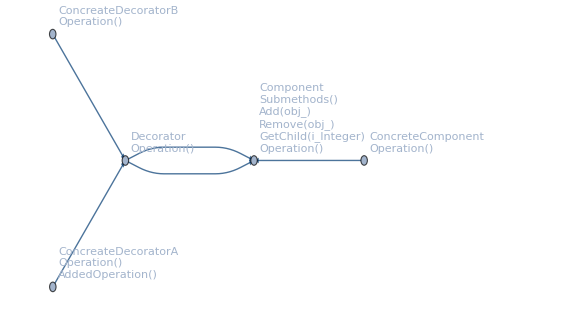

```mathematica
UMLClassGraph[{Component,ConcreteComponent,ConcreateDecoratorA,ConcreateDecoratorB,Decorator}, {Component -> {"Operation"}},{},{Decorator<->Component}, "Abstract" -> {Component},"EntityColumn"->False, VertexLabelStyle -> "Text", ImageSize -> Large,GraphLayout->{"PackingLayout"->"LayeredTop"}]
AutoCollapse[]
```

### Implementation

```mathematica
Clear[Component,ConcreteComponent,ConcreateDecoratorA,ConcreateDecoratorB,Decorator];
```

```mathematica
SELFHEAD=Component;
Component[d_]["Operation"[]]:=Print["error"]
```

```mathematica
Decorator[d_,component_][s_]:=Block[{SELFHEAD=Component},component[s]]
Decorator[d_,component_]["Operation"[]]:=(Print["Decorator:",Head[component]];component["Operation"[]]);
```

```mathematica
ConcreteComponent[d_][s_]:=Block[{SELFHEAD=ConcreteComponent},Component[d][s]]
ConcreteComponent[d_]["Operation"[]]:=Total[Flatten@{d}];
```

```mathematica
ConcreateDecoratorA[d_,component_][s_]:=Block[{SELFHEAD=ConcreateDecoratorA},Decorator[d,component][s]]
ConcreateDecoratorA[d_,component_]["Operation"[]]:=Decorator[d,component]["Operation"[]]^d[[1]];
ConcreateDecoratorA[d_,component_]["AddedOperation"[]]:=Decorator[d,component]["Operation"[]]^2;
```

```mathematica
ConcreateDecoratorB[d_,component_][s_]:=Block[{SELFHEAD=ConcreateDecoratorB},Decorator[d,component][s]]
ConcreateDecoratorB[d_,component_]["Operation"[]]:=1/Decorator[d,component]["Operation"[]];
```

### Experiments

First we create concrete components.

```mathematica
cc=ConcreteComponent[{a,b,c}];
cc["Operation"[]]
```

a+b+c

```mathematica
cdA=ConcreateDecoratorA[{h},cc];
cdA["Operation"[]]
cdA["AddedOperation"[]]
```

Decorator:ConcreteComponent

(a+b+c)^h

Decorator:ConcreteComponent

(a+b+c)^2

Next we create concrete decorators that wrap around the component objects.

```mathematica
cdB=ConcreateDecoratorB[{},cc];
cdB["Operation"[]]
```

Decorator:ConcreteComponent

1/(a+b+c)

```mathematica
cdAB=ConcreateDecoratorB[cdA[[1]],cdA];
cdAB["Operation"[]]
```

Decorator:ConcreateDecoratorA

Decorator:ConcreteComponent

(a+b+c)^-h

```mathematica
cdAABA=ConcreateDecoratorA[{f},ConcreateDecoratorA[{g},ConcreateDecoratorB[{},ConcreateDecoratorA[{h},cc]]]];
cdAABA["Operation"[]]
```

Decorator:ConcreateDecoratorA

Decorator:ConcreateDecoratorB

Decorator:ConcreateDecoratorA

Decorator:ConcreteComponent

(((a+b+c)^-h)^g)^f

### Other concrete examples

In [6] Decorator was used to implement a Single Instruction Multiple Data (SIMD) parallel algorithm for handling the simulations.

GitHubData objects use Decorator for changing of the font styles and the colors of graphs and charts. See [8].

## Observer

The design pattern Observer is fully implemented and supported in Mathematica through the functionalities of Dynamic, Manipulate, and related functions. Here for didactic purposes we show an implementation that predates the introduction of Dynamic (in version 6.0).

The design pattern Observer is also known as Model-View-Controller (MVC).

### The MVC functionality within Mathematica

Here is a slightly modified version an example from the function page for Dynamic:

```mathematica
DynamicModule[{angle = 0, p = {1, 0}}, {LocatorPane[Dynamic[p, (angle = ArcTan @@ #; p = {Cos[Dynamic[angle]], Sin[Dynamic[angle]]}) &], Graphics[{Circle[], Arrowheads[0.15], Arrow[Dynamic[{{0, 0}, p}]]}, ImageSize -> Tiny], Appearance -> None], InputField[Dynamic[angle],Number]}]
```

The example above allows to change the value in the input field by moving the arrow, and change arrow's direction by changing the input value. (This MVC behavior is similar in spirit to the one in the  motivational example for Observer in [5].)

### UML diagram

For Observer it is beneficial to see not just an structural UML diagram but also an UML interaction sequence diagram, see[5]. Here is shown just a structural one.

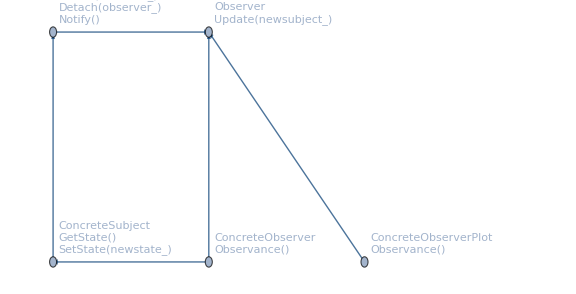

```mathematica
UMLClassGraph[{Subject,ConcreteSubject,Observer,ConcreteObserver,ConcreteObserverPlot}, {Observer -> {"Update"}}, {ConcreteObserver->ConcreteSubject},{Subject->Observer},"Abstract" -> {Subject,Observer},"EntityColumn"->False, VertexLabelStyle ->"Text", ImageSize -> Large,VertexCoordinates->{{1,0},{0,0},{1,1},{2,0},{0,1}}]
AutoCollapse[]
```

### Implementation

```mathematica
ClearAll[Subject,ConcreteSubject,Observer,ConcreteObserver,ConcreteObserverPlot];
```

```mathematica
SUBJECTHEAD=Subject;
(*SetAttributes[Subject,HoldAll]*)
Subject[id_Symbol]["GetObservers"[]]:=SUBJECTHEAD[id]["Observers"];
Subject[id_Symbol]["Attach"[observer_]]:=(SUBJECTHEAD[id]["Observers"]=Append[SUBJECTHEAD[id]["Observers"],observer]);
Subject[id_Symbol]["Detach"[observer_]]:=(SUBJECTHEAD[id]["Observers"]=DeleteCases[SUBJECTHEAD[id]["Observers"],observer]);
Subject[id_Symbol]["Notify"[]]:=Through[(SUBJECTHEAD[id]["Observers"])["Update"[]]];
```

```mathematica
ConcreteSubject[d___][s_]:=Block[{SUBJECTHEAD=ConcreteSubject},Subject[d][s]];
ConcreteSubject[id_Symbol,observers_]:=Block[{},ConcreteSubject[id]["Observers"]=observers;ConcreteSubject[id]];
ConcreteSubject[id_Symbol]["Data"]:={};
ConcreteSubject[id_Symbol]["GetState"[]]:=ConcreteSubject[id]["Data"];ConcreteSubject[id_Symbol]["SetState"[newstate_]]:=(ConcreteSubject[id]["Data"]=newstate);
```

```mathematica
OBSERVERHEAD=Observer;
Observer[id_Symbol]["SetSubject"[newsubject_]]:=(OBSERVERHEAD[id]["Subject"]=newsubject);
Observer[id_Symbol]["GetSubject"[]]:=OBSERVERHEAD[id]["Subject"];
```

```mathematica
ConcreteObserver[id_Symbol,subject_]:=Block[{},ConcreteObserver[id]["Subject"]=subject;ConcreteObserver[id]];
ConcreteObserver[d___][s_]:=Block[{OBSERVERHEAD=ConcreteObserver},Observer[d][s]];
ConcreteObserver[id_Symbol]["Update"[]]:=Grid[{{"observer id","output"},{id,ConcreteObserver[id]["GetSubject"[]]["GetState"[]]}},Dividers->All];
```

```mathematica
ConcreteObserverPlot[id_Symbol,subject_]:=Block[{},ConcreteObserverPlot[id]["Subject"]=subject;ConcreteObserverPlot[id]];
ConcreteObserverPlot[d___][s_]:=Block[{OBSERVERHEAD=ConcreteObserverPlot},Observer[d][s]];
ConcreteObserverPlot[id_Symbol]["Update"[]]:=Grid[{{"observer id","output"},{id,Apply[Plot,ConcreteObserverPlot[id]["GetSubject"[]]["GetState"[]]]}},Dividers->All];
```

### Experiments

First let us we create a concrete subject to be observed.

```mathematica
ClearAll[csubj]
csubj=ConcreteSubject[Unique[],{}]
```

ConcreteSubject[$173]

The signature of the creating function is such that it has the head of the concrete subject class ConcreteSubject and it takes two arguments, an identifier symbol and a list of observers (that can be empty). The creator function returns a ConcreteSubject object.

Next we are going to set a state for the concrete subject.

```mathematica
csubj["SetState"[{Sin[x],{x,0,π}}]];
csubj["GetState"[]]
```

{Sin[x],{x,0,π}}

Let us create two concrete Observer objects, one for printing the state of the subject, the other for plotting the state of the subject.

```mathematica
ClearAll[ob,obp];
ob=ConcreteObserver[Unique[],csubj];
obp=ConcreteObserverPlot[Unique[],csubj];
```

What the creator functions of the observers do parallels what the creator for concrete subject objects does. The signature of each creating function is such that it has the head of the concrete observer class and it takes two arguments, an identifier symbol and a list of subjects (that can be empty). The creator functions return the corresponding concrete observer objects.

Next we attach the observers to the subject.

```mathematica
csubj["Attach"[ob]];
csubj["Attach"[obp]];
```

```mathematica
csubj["GetObservers"[]]
```

{ConcreteObserver[$174],ConcreteObserverPlot[$175]}

This command retrieves the current state of the subject:

```mathematica
csubj["GetState"[]]
```

{Sin[x],{x,0,π}}

The following command notifies the observers attached to the subject about its state. The result is a list of the observers views on the subject’s state.

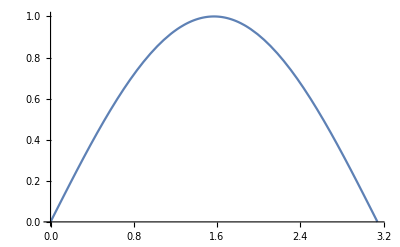
{observer id | output
$174 | {Sin[x],{x,0,π}},observer id | output
$175 | -Graphics-}

```mathematica
csubj["Notify"[]]
```

Let us change the state of the subject to something else.

```mathematica
csubj["SetState"[{Cos[x],{x,0,2π}}]]
```

{Cos[x],{x,0,2 π}}

And let us notify the attached observers to react to the state change.

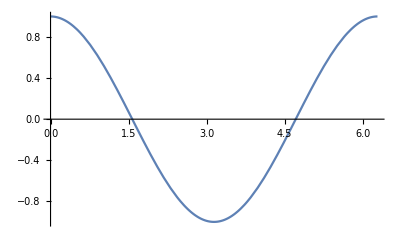
{observer id | output
$174 | {Cos[x],{x,0,2 π}},observer id | output
$175 | -Graphics-}

```mathematica
csubj["Notify"[]]
```

## Interpreter

The design pattern Interpreter prescribes how to implement interpretation of (small and context free) languages. The intent given in [5] is:

Given a language, define a representation for its grammar along with an interpreter that uses the representation to interpret sentences in the language.

Interpreter is a powerful design pattern that allows to approach the solution of re-occurring problems using Domain Specific Languages (DSL’s).

### UML diagram

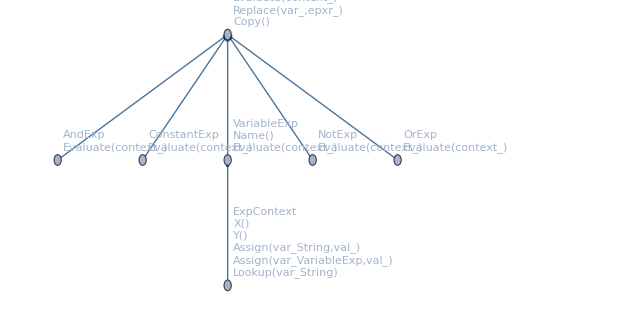

```mathematica
If[True,
UMLClassGraph[{BooleanExp,VariableExp,ConstantExp,AndExp,OrExp,NotExp,ExpContext},{BooleanExp->{BooleanExp,"Evaluate","Replace","Copy"}},{ExpContext->VariableExp},
"EntityColumn"->False, VertexLabelStyle -> "Text", ImageSize -> Large,GraphLayout->"LayeredEmbedding"],UMLClassGraph[{BooleanExp,VariableExp,ConstantExp,AndExp,OrExp,NotExp,ExpContext,Client},{BooleanExp->{BooleanExp,"Evaluate","Replace","Copy"}},{ExpContext<->VariableExp,Client->ExpContext,Client->BooleanExp},
"EntityColumn"->False, VertexLabelStyle -> "Text", ImageSize -> Medium,GraphLayout->"LayeredEmbedding"]
]
AutoCollapse[]
```

### Backus-Naur Form (BNF)

The implementation -- and explanation -- of the design pattern Interpreter is based on the Backus-Naur Form (BNF). For each BNF rule we program a class that provides an interpretation for it. Interpreter traverses a tree of linked objects corresponding to the BNF rules.

Here is the BNF of a DSL for handling Boolean expressions of a certain type:

BooleanExp::=VariableExp|Constant|OrExp|AndExp|NotExp|'(' BooleanExp')'
AndExp::=BooleanExp'and' BooleanExp
OrExp::=BooleanExp'or' BooleanExp
NotExp::='not' BooleanExp
Constant::='true'|'false'
VariableExp::='A'|'B'|...|'X'|'Y'|'Z'

### Implementation

The implementation follows the BNF in the previous section.

```mathematica
Clear[BooleanExp,VariableExp,ConstantExp,AndExp,OrExp,NotExp]
```

```mathematica
SELFHEAD=BooleanExp;
BooleanExp[d___]["Data"[]]:=d;
BooleanExp[d___]["Evaluate"[context_]]:=Null;
BooleanExp[d___]["Replace"[var_,epxr_]]:=Null;
BooleanExp[d___]["Copy"[]]:=Null;
```

```mathematica
VariableExp[d___][s_]:=Block[{SELFHEAD=VariableExp},BooleanExp[d][s]]
VariableExp[{var_String,rest___}]["Name"[]]:=var;VariableExp[{var_String,rest___}]["Evaluate"[context_]]:=context["Lookup"[var]];
```

```mathematica
ConstantExp[d___][s_]:=Block[{SELFHEAD=ConstantExp},BooleanExp[d][s]]
ConstantExp[{val_,rest___}]["Evaluate"[context_]]:=If[val==="true",True,False];
```

```mathematica
AndExp[d___][s_]:=Block[{SELFHEAD=AndExp},BooleanExp[d][s]]
AndExp[{operand1_,operand2_,rest___}]["Evaluate"[context_]]:=operand1["Evaluate"[context]]&&operand2["Evaluate"[context]];
```

```mathematica
OrExp[d___][s_]:=Block[{SELFHEAD=OrExp},BooleanExp[d][s]]
OrExp[{operand1_,operand2_,rest___}]["Evaluate"[context_]]:=operand1["Evaluate"[context]]||operand2["Evaluate"[context]];
```

```mathematica
NotExp[d___][s_]:=Block[{SELFHEAD=NotExp},BooleanExp[d][s]]
NotExp[{operand1_,rest___}]["Evaluate"[context_]]:=Not[operand1["Evaluate"[context]]];
```

```mathematica
Clear[ExpContext]
ExpContext[d_]["Assign"[var_String,val_]]:=ExpContext[d][var[]]=val;
ExpContext[d_]["Assign"[var_VariableExp,val_]]:=Module[{name=var["Name"[]]},ExpContext[d][name[]]=val];ExpContext[d_]["Lookup"[var_String]]:=ExpContext[d][var[]]
```

Dummy client class for the UML diagram.

```mathematica
Clear[Client]
Client[___]["Operation"[context_ExpContext,expr_BooleanExp,___]]:=expr["Evaluate"[context]]
Client[{context_ExpContext,expr_}]["Evaluate"]:=expr["Evaluate"[context]]
```

### Experiments

(true and x) or (y and (not x))

```mathematica
tr=ConstantExp[{"true"}];
fl=ConstantExp[{"false"}];
x=VariableExp[{"X"}];
y=VariableExp[{"Y"}];
orexp=OrExp[{AndExp[{tr,x}],AndExp[{y,NotExp[{x}]}]}];
```

```mathematica
Clear[cont]
cont=ExpContext["first"];
cont["Assign"[x,False]]
cont["Assign"[y,False]]
```

False

False

```mathematica
orexp["Evaluate"[cont]]
```

False

```mathematica
texp=OrExp[{y,NotExp[{x}]}];
```

```mathematica
texp["Evaluate"[cont]]
```

True

### Other concrete examples

I designed and implemented NIntegrate’s Method option using the Interpreter design pattern. (That design was also applied to NSum.) See [9] for brief details.

### Extension

Interpreter is probably my favorite design pattern and I have extended it with the package FunctionalParsers.m, [11]. With that package we can overcome one of the serious limitations of Interpreter, its applicability to simple grammars, [5]. A sufficiently complex and concise application of the package FunctionalParsers.m is given in my blog post "Natural language processing with functional parsers", [12].

For example here is the Extended BNF (EBNF) of a simple grammar for expressing food desires:

```mathematica
ebnfCode="
<lovefood> = <subject> , <loveverb> , <object-spec> ;
<loveverb> = ( 'love' | 'crave' | 'demand' ) <@ LoveType ;
<object-spec> = ( <object-list> | <object> | <objects> | 'Range[2,100]' , <objects> ) <@ LoveObjects ;
<subject> = 'i' | 'we' | 'you' <@ Who ; 
<object> = 'sushi' | [ 'a' ] , 'chocolate' | 'milk' | [ 'an' , 'ice' ] , 'cream' | 'a' , 'tangerine' ;
<objects> = 'sushi' | 'chocolates' | 'milks' | 'ice' , 'creams' | 'tangerines' ; 
<object-list> = ( <object> | <objects> ) , { 'and' ⊳ ( <object> | <objects> ) } ; ";
```

This command generates the grammar parsers:

```mathematica
GenerateParsersFromEBNF[ToTokens@ebnfCode];
```

These commands show the parsing of different sentences of the grammar defined above:

```mathematica
sentences={"I love sushi","We demand 2 ice creams","You crave chocolate and milk"};
Magnify[#,0.8]&@
ParsingTestTable[pLOVEFOOD,ToLowerCase@sentences,"Layout"->"Vertical"]
```

1 | command: | i love sushi
 | parsed: | {Who[i],{LoveType[love],LoveObjects[{sushi,{}}]}}
 | residual: | {}
2 | command: | we demand 2 ice creams
 | parsed: | {Who[we],{LoveType[demand],LoveObjects[{2,{ice,creams}}]}}
 | residual: | {}
3 | command: | you crave chocolate and milk
 | parsed: | {Who[you],{LoveType[crave],LoveObjects[{{{},chocolate},{milk}}]}}
 | residual: | {}

At this point it is easy enough to develop interpreters for the parsed sentences.

## Future plans

1. Implement the generation of UML object interaction sequence diagrams using Design Patterns implementations (in Mathematica).

2. Implement code generation based on specified Design Patterns. It is especially interesting the code generation to be specified by natural language sentences describing the system architecture.

3. Investigate discovering design patterns within existing code.

## References

[1] Christopher Alexander et al., The Oregon Experiment, Oxford University Press, 1975.

[2] Christopher Alexander et al., A Pattern Language - Towns, Buildings, Construction, Oxford University Press, 1977.

[3] Christopher Alexander, The Timeless Way of Building, Oxford University Press, 1979.

[4] Kent Beck, Ward Cunningham, “Using Pattern Languages for Object-Oriented Programs”, OOPSLA-87, (1987).

[5] Erich Gamma, Richard Helm, Ralph Johnson, John Vlissides, Design Patterns: Elements of Reusable Object-Oriented Software, Addison-Wesley, 1994.

[6] Anton Antonov, Air pollution modeling with gridMathematica, Wolfram Technology Conference 2006. URL: http://library.wolfram.com/infocenter/Conferences/6532/ .

[7] Anton Antonov, GitHubPlots, Mathematica package, MathematicaForPrediction at GitHub, 2015. URL: https://github.com/antononcube/MathematicaForPrediction/blob/master/Misc/GitHubPlots.m .

[8] Anton Antonov, GitHubObjects, Mathematica package, MathematicaForPrediction at GitHub, 2015. URL: https://github.com/antononcube/MathematicaForPrediction/blob/master/Misc/GitHubDataObjects.m .

[9] Anton Antonov, Object Oriented Design Patterns, Wolfram Technology Conference 2015. URL: http://www.wolfram.com/broadcast/video.php?c=400&v=1470 .

[10] Anton Antonov, UML Diagram Generation,  Mathematica package, MathematicaForPrediction at GitHub, 2016. URL: https://github.com/antononcube/MathematicaForPrediction/blob/master/Misc/UMLDiagramGeneration.m.

[11] Anton Antonov, Functional parsers, Mathematica package, MathematicaForPrediction at GitHub, 2014. URL: https://github.com/antononcube/MathematicaForPrediction/blob/master/FunctionalParsers.m .

[12] Anton Antonov, “Natural language processing with functional parsers”, (2014), MathematicaForPrediction at WordPress blog. URL: https://mathematicaforprediction.wordpress.com/2014/02/13/natural-language-processing-with-functional-parsers/ .

[13]  Anton Antonov, Object-oriented framework for large scale air pollution models, 2001. Ph.D. thesis, Informatics and Mathematical Modelling, Technical University of Denmark, DTU.

Related Guides

Book Chapters

Related Tech Notes

Monad code generation and extension

## Metadata

### Categorization

Tech Note

AntonAntonov/SoftwareDesignMethodsWithWLBook

AntonAntonov`SoftwareDesignMethodsWithWLBook`

AntonAntonov/SoftwareDesignMethodsWithWLBook/tutorial/ImplementationofOOPDesignPatternsinWL

### Keywords